```mathematica
Quit
```

```mathematica
clear[Subscript[G, 1],Subscript[G, 2],Subscript[η, 1],Subscript[η, 2],Subscript[η, 3],Subscript[η, 4]]
```

clear[G_1,G_2,η_1,η_2,η_3,η_4]

```mathematica
ClearAll["Global`*"]
```

```mathematica
rni2ns2ns1 = ((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))
```

((-1+G_1) (-1+(1+2 α^2) G_1) η_2^2+(-1+G_2)^2 (1+η_1 (-2-2 α^2+(1+2 α^2) G_1+η_1+(-1+G_1) (-2 α^2+G_1+2 α^2 G_1) η_1)) η_3^2+(-1+η_4) η_4+G_2^2 (1+(-1+G_1) η_1) (1+(1+2 α^2) (-1+G_1) η_1) η_4^2-2 α^2 √(G_2 η_3) √((-1+G_1) (-1+G_2) η_1 η_3) √((-1+G_2) η_4) √((-1+G_1) G_2 η_1 η_4)-2 √(-((-1+G_2) (-1+η_1) η_3)) √((-1+G_1) (-1+G_2) η_1 η_3) √(-G_2 (-1+η_1) η_4) √((-1+G_1) G_2 η_1 η_4)-2 α^2 √(-((-1+G_2) (-1+η_1) η_3)) √((-1+G_1) (-1+G_2) η_1 η_3) √(-G_2 (-1+η_1) η_4) √((-1+G_1) G_2 η_1 η_4)+2 α^2 √((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4)-2 √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4)-2 α^2 √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4)-G_2 (1+(1+α^2) (-1+G_1) η_1) η_4 (-1+2 η_4)-2 (√((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3)+α^2 √((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) (-1+G_2) η_1 η_3) √(G_1 (-1+G_2) η_1 η_3)+√(G_2 η_3) √(-((-1+G_2) (-1+η_1) η_3)) √((-1+G_2) η_4) √(-G_2 (-1+η_1) η_4)+√(G_2 η_3) √(G_1 (-1+G_2) η_1 η_3) √((-1+G_2) η_4) √(G_1 G_2 η_1 η_4)-√((-1+G_1) η_2) √(G_1 η_2) √((-1+G_1) G_2 η_1 η_4) √(G_1 G_2 η_1 η_4))+(-1+G_2) η_3 (1+(-1+G_1) η_1 (1+α^2-2 α^2 (-1+G_1) G_2 η_1 η_4))+η_2 (-1+G_1 (1+α^2-2 α^2 (-1+G_1) η_1 ((-1+G_2) η_3-G_2 η_4))))/((-1+(1+α^2) G_1) η_2-η_4+(1+(1+α^2) (-1+G_1) η_1) ((-1+G_2) η_3+G_2 η_4))

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 5.6;
α = 4;

ra1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(21.568+(2.153×10^-15) G_2-(1.794×10^-15) G_2^2)/(0.088+1.000 G_2)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 0.78;
Subscript[G, 1] = 5.6;
α = 4;

ra2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(24.232-5.007 G_2+0.294 G_2^2)/(0.101+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.93;
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.98;
Subscript[η, 4] = 0.74;
Subscript[G, 1] = 5.6;
α = 4;

ra3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(19.746-4.809 G_2+0.338 G_2^2)/(0.019+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.82;
Subscript[η, 2] = 0.87;
Subscript[η, 3] = 0.93;
Subscript[η, 4] = 0.64;
Subscript[G, 1] = 5.6;
α = 4;

ra4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(22.556-6.107 G_2+0.486 G_2^2)/(0.203+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.92;
Subscript[η, 2] = 0.63;
Subscript[η, 3] = 0.96;
Subscript[η, 4] = 0.72;
Subscript[G, 1] = 5.6;
α = 4;

ra5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(15.900-4.308 G_2+0.343 G_2^2)/(-0.093+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.92;
Subscript[η, 2] = 0.63;
Subscript[η, 3] = 0.96;
Subscript[η, 4] = 0.76;
Subscript[G, 1] = 5.6;
α = 4;

ra6 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(15.531-3.489 G_2+0.232 G_2^2)/(-0.091+1.000 G_2)

```mathematica
Subscript[η, 1] = 0.92;
Subscript[η, 2] = 0.63;
Subscript[η, 3] = 0.96;
Subscript[η, 4] = 0.87;
Subscript[G, 1] = 5.6;
α = 4;

ra7 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(14.598-1.439 G_2+0.042 G_2^2)/(-0.087+1.000 G_2)

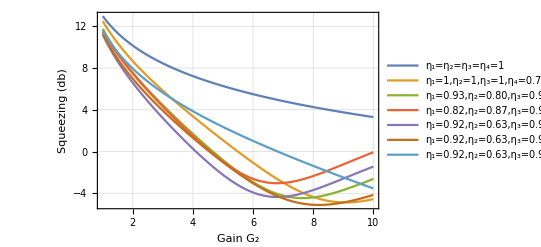

```mathematica
Plot[{10Log10[("21.568"+("2.153"×10^("-15")) Subscript[G, "2"]-("1.794"×10^("-15")) Subscript[G, "2"]^("2"))/("0.088"+"1.000" Subscript[G, "2"])](*1, 1, 1*),10Log10[("24.232"-"5.007" Subscript[G, "2"]+"0.294" Subscript[G, "2"]^("2"))/("0.101"+"1.000" Subscript[G, "2"])](*0.9, 0.9, 0.9*),10Log10[("19.746"-"4.809" Subscript[G, "2"]+"0.338" Subscript[G, "2"]^("2"))/("0.019"+"1.000" Subscript[G, "2"])],10Log10[("22.556"-"6.107" Subscript[G, "2"]+"0.486" Subscript[G, "2"]^("2"))/("0.203"+"1.000" Subscript[G, "2"])],10Log10[("15.900"-"4.308" Subscript[G, "2"]+"0.343" Subscript[G, "2"]^("2"))/("-0.093"+"1.000" Subscript[G, "2"])](*0.8, 0.85, 0.7*),10Log10[("15.531"-"3.489" Subscript[G, "2"]+"0.232" Subscript[G, "2"]^("2"))/("-0.091"+"1.000" Subscript[G, "2"])],10Log10[("14.598"-"1.439" Subscript[G, "2"]+"0.042" Subscript[G, "2"]^("2"))/("-0.087"+"1.000" Subscript[G, "2"])]},{Subscript[G, 2],1,10},PlotStyle->ScientificForm(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),PlotLegends->{"η_1=η_2=η_3=η_4=1","η_1=1,η_2=1,η_3=1,η_4=0.78","η_1=0.93,η_2=0.80,η_3=0.98,η_4=0.74","η_1=0.82,η_2=0.87,η_3=0.93,η_4=0.64","η_1=0.92,η_2=0.63,η_3=0.96,η_4=0.72","η_1=0.92,η_2=0.63,η_3=0.96,η_4=0.76","η_1=0.92,η_2=0.63,η_3=0.96,η_4=0.87"},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["Gain G_2"],HoldForm["R_(ni2 - ns2 - ns1) vs G_2 for G_1 = 5.6, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
squeezing Vs. Subscript[η, 1]:-
```

```mathematica
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rb1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(56+36 η_1+69 η_1^2)/(29+110 η_1)

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rb2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.355-0.070 η_1+0.454 η_1^2)/(0.234+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rb3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.534-0.509 η_1+0.690 η_1^2)/(0.280+1.000 η_1)

```mathematica
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;
rb4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(7 (8+2 η_1+13 η_1^2))/(31+130 η_1)

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

rb5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.395-0.347 η_1+0.588 η_1^2)/(0.241+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

rb6 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.339-0.442 η_1+0.612 η_1^2)/(0.222+1.000 η_1)

```mathematica
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rb7 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(56-12 η_1+117 η_1^2)/(33+150 η_1)

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rb8 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.351-0.443 η_1+0.720 η_1^2)/(0.222+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rb9 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.301-0.556 η_1+0.745 η_1^2)/(0.206+1.000 η_1)

```mathematica
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rb10 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(7 (8-6 η_1+21 η_1^2))/(5 (7+34 η_1))

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rb11 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.318-0.525 η_1+0.855 η_1^2)/(0.208+1.000 η_1)

```mathematica
Subscript[η, 2] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rb12 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(0.272-0.656 η_1+0.882 η_1^2)/(0.193+1.000 η_1)

```mathematica
rb10
rb11
rb12
```

(7 (8-6 η_1+21 η_1^2))/(5 (7+34 η_1))

(0.318-0.525 η_1+0.855 η_1^2)/(0.208+1.000 η_1)

(0.272-0.656 η_1+0.882 η_1^2)/(0.193+1.000 η_1)

```mathematica
g1 = Plot[{10Log10[("56"+"36" Subscript[η, "1"]+"69" Subscript[η, "1"]^("2"))/("29"+"110" Subscript[η, "1"])](*0.9, 0.9*),10Log10[("0.355"-"0.070" Subscript[η, "1"]+"0.454" Subscript[η, "1"]^("2"))/("0.234"+"1.000" Subscript[η, "1"])](*0.8, 0.7*),10Log10[("0.534"-"0.509" Subscript[η, "1"]+"0.690" Subscript[η, "1"]^("2"))/("0.280"+"1.000" Subscript[η, "1"])]},{Subscript[η, 1],0.1,1},PlotLegends->{"η_2=η_3=η_4=1","η_2=0.7,η_3=0.9,η_4=0.8","η_2=0.8,η_3=0.9,η_4=0.6"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["for G_1= 2, G_2= 6, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g2 = Plot[{10Log10[("7" ("8"+"2" Subscript[η, "1"]+"13" Subscript[η, "1"]^("2")))/("31"+"130" Subscript[η, "1"])](*0.9, 0.9*),10Log10[("0.395"-"0.347" Subscript[η, "1"]+"0.588" Subscript[η, "1"]^("2"))/("0.241"+"1.000" Subscript[η, "1"])](*0.8, 0.7*),10Log10[("0.339"-"0.442" Subscript[η, "1"]+"0.612" Subscript[η, "1"]^("2"))/("0.222"+"1.000" Subscript[η, "1"])]},{Subscript[η, 1],0.1,1},PlotLegends->{"η_2=η_3=η_4=1","η_2=0.7,η_3=0.8,η_4=0.6","η_2=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["for G_1= 2, G_2= 7, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g3 = Plot[{10Log10[("56"-"12" Subscript[η, "1"]+"117" Subscript[η, "1"]^("2"))/("33"+"150" Subscript[η, "1"])](*0.9, 0.9*),10Log10[("0.351"-"0.443" Subscript[η, "1"]+"0.720" Subscript[η, "1"]^("2"))/("0.222"+"1.000" Subscript[η, "1"])](*0.8, 0.7*),10Log10[("0.301"-"0.556" Subscript[η, "1"]+"0.745" Subscript[η, "1"]^("2"))/("0.206"+"1.000" Subscript[η, "1"])]},{Subscript[η, 1],0.1,1},PlotLegends->{"η_2=η_3=η_4=1","η_2=0.7,η_3=0.8,η_4=0.6","η_2=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["for G_1= 2, G_2= 8, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g4 = Plot[{10Log10[("7" ("8"-"6" Subscript[η, "1"]+"21" Subscript[η, "1"]^("2")))/("5" ("7"+"34" Subscript[η, "1"]))](*0.9, 0.9*),10Log10[("0.318"-"0.525" Subscript[η, "1"]+"0.855" Subscript[η, "1"]^("2"))/("0.208"+"1.000" Subscript[η, "1"])](*0.8, 0.7*),10Log10[("0.272"-"0.656" Subscript[η, "1"]+"0.882" Subscript[η, "1"]^("2"))/("0.193"+"1.000" Subscript[η, "1"])]},{Subscript[η, 1],0.1,1},PlotLegends->{"η_2=η_3=η_4=1","η_2=0.7,η_3=0.8,η_4=0.6","η_2=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["for G_1= 2, G_2= 9, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

GraphicsColumn[{g1,g2,g3,g4}]
```

-Graphics-

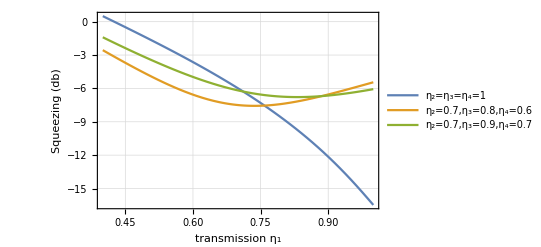

```mathematica
Plot[{10Log10[("1.541"-"2.765" Subscript[η, "1"]+"1.251" Subscript[η, "1"]^("2"))/("0.166"+"1.000" Subscript[η, "1"])](*0.9, 0.9*),10Log10[("1.008"-"2.495" Subscript[η, "1"]+"1.812" Subscript[η, "1"]^("2"))/("0.141"+"1.000" Subscript[η, "1"])](*0.8, 0.7*),10Log10[("1.083"-"2.319" Subscript[η, "1"]+"1.520" Subscript[η, "1"]^("2"))/("0.151"+"1.000" Subscript[η, "1"])]},{Subscript[η, 1],0.4,1},PlotLegends->{"η_2=η_3=η_4=1","η_2=0.7,η_3=0.8,η_4=0.6","η_2=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_1"],HoldForm["R_(ni2 - ns2 - ns1) vs η_1 for G_1= 2, G_2= 9, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
squeezing Vs. Subscript[η, 2]:-
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rc1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(29+95 η_2+37 η_2^2)/(120+19 η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rc2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (0.175+0.945 η_2+η_2^2))/(3.874+η_2)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rc3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (1.376-0.965 η_2+η_2^2))/(3.805+η_2)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;
rc4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(29+95 η_2+37 η_2^2)/(142+19 η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

rc5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (0.825-0.349 η_2+η_2^2))/(3.758+η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

rc6 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (0.571-0.205 η_2+η_2^2))/(4.300+η_2)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rc7 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(29+95 η_2+37 η_2^2)/(164+19 η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rc8 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (1.061-0.637 η_2+η_2^2))/(4.347+η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rc9 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (0.744-0.493 η_2+η_2^2))/(4.974+η_2)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 3] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rc10 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(29+95 η_2+37 η_2^2)/(186+19 η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rc11 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (1.336-0.924 η_2+η_2^2))/(4.937+η_2)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 3] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rc12 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1.947 (0.950-0.781 η_2+η_2^2))/(5.647+η_2)

```mathematica
rc10
rc11
rc12
```

(29+95 η_2+37 η_2^2)/(186+19 η_2)

(1.947 (1.336-0.924 η_2+η_2^2))/(4.937+η_2)

(1.947 (0.950-0.781 η_2+η_2^2))/(5.647+η_2)

```mathematica
g1 = Plot[{10Log10[("29"+"95" Subscript[η, "2"]+"37" Subscript[η, "2"]^("2"))/("120"+"19" Subscript[η, "2"])](*0.9, 0.9*),10Log10[("1.947" ("0.175"+"0.945" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("3.874"+Subscript[η, "2"])](*0.8, 0.7*),10Log10[("1.947" ("1.376"-"0.965" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("3.805"+Subscript[η, "2"])]},{Subscript[η, 2],0.1,1},PlotLegends->{"η_1=η_3=η_4=1","η_1=0.7,η_3=0.9,η_4=0.8","η_1=0.8,η_3=0.9,η_4=0.6"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_2"],HoldForm["for G_1= 2, G_2= 6, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g2 = Plot[{10Log10[("29"+"95" Subscript[η, "2"]+"37" Subscript[η, "2"]^("2"))/("142"+"19" Subscript[η, "2"])](*0.9, 0.9*),10Log10[("1.947" ("0.825"-"0.349" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("3.758"+Subscript[η, "2"])](*0.8, 0.7*),10Log10[("1.947" ("0.571"-"0.205" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("4.300"+Subscript[η, "2"])]},{Subscript[η, 2],0.1,1},PlotLegends->{"η_1=η_3=η_4=1","η_1=0.7,η_3=0.8,η_4=0.6","η_1=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_2"],HoldForm["for G_1= 2, G_2= 7, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g3 = Plot[{10Log10[("29"+"95" Subscript[η, "2"]+"37" Subscript[η, "2"]^("2"))/("164"+"19" Subscript[η, "2"])](*0.9, 0.9*),10Log10[("1.947" ("1.061"-"0.637" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("4.347"+Subscript[η, "2"])](*0.8, 0.7*),10Log10[("1.947" ("0.744"-"0.493" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("4.974"+Subscript[η, "2"])]},{Subscript[η, 2],0.1,1},PlotLegends->{"η_1=η_3=η_4=1","η_1=0.7,η_3=0.8,η_4=0.6","η_1=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_2"],HoldForm["for G_1= 2, G_2= 8, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g4 = Plot[{10Log10[("29"+"95" Subscript[η, "2"]+"37" Subscript[η, "2"]^("2"))/("186"+"19" Subscript[η, "2"])](*0.9, 0.9*),10Log10[("1.947" ("1.336"-"0.924" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("4.937"+Subscript[η, "2"])](*0.8, 0.7*),10Log10[("1.947" ("0.950"-"0.781" Subscript[η, "2"]+Subscript[η, "2"]^("2")))/("5.647"+Subscript[η, "2"])]},{Subscript[η, 2],0.1,1},PlotLegends->{"η_1=η_3=η_4=1","η_1=0.7,η_3=0.8,η_4=0.6","η_1=0.7,η_3=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_2"],HoldForm["for G_1= 2, G_2= 9, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

GraphicsColumn[{g1,g2,g3,g4}]
```

-Graphics-

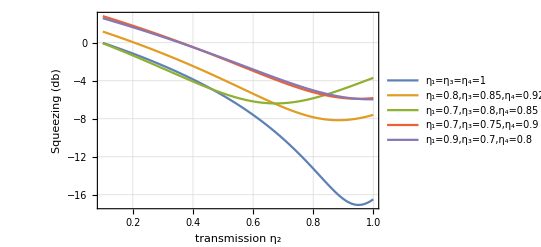

```mathematica
Plot[{10Log10[("8.243"-"17.048" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("6.547"+"1.000" Subscript[η, "2"])](*0.9, 0.9*),10Log10[("7.733"-"15.720" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("4.672"+"1.000" Subscript[η, "2"])](*0.8, 0.7*),10Log10[("4.966"-"11.887" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("3.813"+"1.000" Subscript[η, "2"])],10Log10[("9.105"-"16.814" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("3.843"+"1.000" Subscript[η, "2"])],10Log10[("9.930"-"17.518" Subscript[η, "2"]+"8.975" Subscript[η, "2"]^("2"))/("4.462"+"1.000" Subscript[η, "2"])](*0.8, 0.6*)},{Subscript[η, 2],0.1,1},PlotLegends->{"η_1=η_3=η_4=1","η_1=0.8,η_3=0.85,η_4=0.92","η_1=0.7,η_3=0.8,η_4=0.85","η_1=0.7,η_3=0.75,η_4=0.9","η_1=0.9,η_3=0.7,η_4=0.8"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_2"],HoldForm["R_(ni2 - ns2 - ns1) vs η_2 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
squeezing Vs. Subscript[η, 3]:-
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rd1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1886-2725 η_3+1000 η_3^2)/(84+55 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 4] = 0.8;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rd2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(20.345-34.157 η_3+14.931 η_3^2)/(1.368+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 2] = 0.9;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

rd3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(13.672-28.408 η_3+16.022 η_3^2)/(1.087+1.000 η_3)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;
rd4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(2471-3750 η_3+1440 η_3^2)/(95+66 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

rd5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(13.323-29.846 η_3+17.918 η_3^2)/(1.004+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

rd6 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(17.697-34.765 η_3+17.918 η_3^2)/(1.158+1.000 η_3)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rd7 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(7 (448-705 η_3+280 η_3^2))/(106+77 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rd8 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(14.203-33.492 η_3+20.904 η_3^2)/(0.946+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

rd9 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(18.918-39.019 η_3+20.904 η_3^2)/(1.093+1.000 η_3)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 4] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rd10 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(3881-6280 η_3+2560 η_3^2)/(117+88 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.8;
Subscript[η, 4] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rd11 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(15.136-37.139 η_3+23.890 η_3^2)/(0.903+1.000 η_3)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 4] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

rd12 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(20.206-43.273 η_3+23.890 η_3^2)/(1.044+1.000 η_3)

```mathematica
rd7
rd8
rd9
```

(7 (448-705 η_3+280 η_3^2))/(106+77 η_3)

(14.203-33.492 η_3+20.904 η_3^2)/(0.946+1.000 η_3)

(18.918-39.019 η_3+20.904 η_3^2)/(1.093+1.000 η_3)

```mathematica
g1 = Plot[{10Log10[("1886"-"2725" Subscript[η, "3"]+"1000" Subscript[η, "3"]^("2"))/("84"+"55" Subscript[η, "3"])](*0.9, 0.9*),10Log10[("20.345"-"34.157" Subscript[η, "3"]+"14.931" Subscript[η, "3"]^("2"))/("1.368"+"1.000" Subscript[η, "3"])](*0.8, 0.7*),10Log10[("13.672"-"28.408" Subscript[η, "3"]+"16.022" Subscript[η, "3"]^("2"))/("1.087"+"1.000" Subscript[η, "3"])]},{Subscript[η, 3],0.1,1},PlotLegends->{"η_1=η_2=η_4=1","η_1=0.7,η_2=0.9,η_4=0.8","η_1=0.8,η_2=0.9,η_4=0.6"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["for G_1= 2, G_2= 6, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g2 = Plot[{10Log10[("2471"-"3750" Subscript[η, "3"]+"1440" Subscript[η, "3"]^("2"))/("95"+"66" Subscript[η, "3"])](*0.9, 0.9*),10Log10[("13.323"-"29.846" Subscript[η, "3"]+"17.918" Subscript[η, "3"]^("2"))/("1.004"+"1.000" Subscript[η, "3"])](*0.8, 0.7*),10Log10[("17.697"-"34.765" Subscript[η, "3"]+"17.918" Subscript[η, "3"]^("2"))/("1.158"+"1.000" Subscript[η, "3"])]},{Subscript[η, 3],0.1,1},PlotLegends->{"η_1=η_2=η_4=1","η_1=0.7,η_2=0.8,η_4=0.6","η_1=0.7,η_2=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["for G_1= 2, G_2= 7, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g3 = Plot[{10Log10[("7" ("448"-"705" Subscript[η, "3"]+"280" Subscript[η, "3"]^("2")))/("106"+"77" Subscript[η, "3"])](*0.9, 0.9*),10Log10[("14.203"-"33.492" Subscript[η, "3"]+"20.904" Subscript[η, "3"]^("2"))/("0.946"+"1.000" Subscript[η, "3"])](*0.8, 0.7*),10Log10[("18.918"-"39.019" Subscript[η, "3"]+"20.904" Subscript[η, "3"]^("2"))/("1.093"+"1.000" Subscript[η, "3"])]},{Subscript[η, 3],0.1,1},PlotLegends->{"η_1=η_2=η_4=1","η_1=0.7,η_2=0.8,η_4=0.6","η_1=0.7,η_2=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["for G_1= 2, G_2= 8, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g4 = Plot[{10Log10[("3881"-"6280" Subscript[η, "3"]+"2560" Subscript[η, "3"]^("2"))/("117"+"88" Subscript[η, "3"])](*0.9, 0.9*),10Log10[("15.136"-"37.139" Subscript[η, "3"]+"23.890" Subscript[η, "3"]^("2"))/("0.903"+"1.000" Subscript[η, "3"])](*0.8, 0.7*),10Log10[("20.206"-"43.273" Subscript[η, "3"]+"23.890" Subscript[η, "3"]^("2"))/("1.044"+"1.000" Subscript[η, "3"])]},{Subscript[η, 3],0.1,1},PlotLegends->{"η_1=η_2=η_4=1","η_1=0.7,η_2=0.8,η_4=0.6","η_1=0.7,η_2=0.9,η_4=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["for G_1= 2, G_2= 9, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

GraphicsColumn[{g1,g2,g3,g4}]
```

-Graphics-

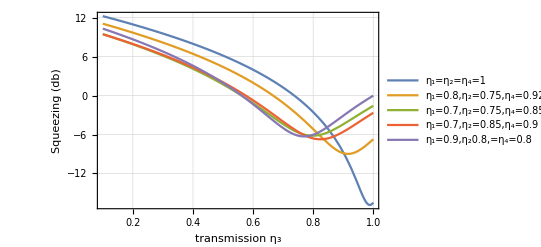

```mathematica
Plot[{10Log10[("35.935"-"72.609" Subscript[η, "3"]+"36.734" Subscript[η, "3"]^("2"))/("1.640"+"1.000" Subscript[η, "3"])](*0.9, 0.9*),10Log10[("25.869"-"55.939" Subscript[η, "3"]+"30.604" Subscript[η, "3"]^("2"))/("1.513"+"1.000" Subscript[η, "3"])](*0.8, 0.7*),10Log10[("17.905"-"43.728" Subscript[η, "3"]+"27.538" Subscript[η, "3"]^("2"))/("1.468"+"1.000" Subscript[η, "3"])],10Log10[("19.030"-"45.166" Subscript[η, "3"]+"27.538" Subscript[η, "3"]^("2"))/("1.582"+"1.000" Subscript[η, "3"])],10Log10[("20.278"-"51.616" Subscript[η, "3"]+"33.670" Subscript[η, "3"]^("2"))/("1.343"+"1.000" Subscript[η, "3"])](*0.8, 0.6*)},{Subscript[η, 3],0.1,1},PlotLegends->{"η_1=η_2=η_4=1","η_1=0.8,η_2=0.75,η_4=0.92","η_1=0.7,η_2=0.75,η_4=0.85","η_1=0.7,η_2=0.85,η_4=0.9","η_1=0.9,η_20.8,=η_4=0.8"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_3"],HoldForm["R_(ni2 - ns2 - ns1) vs η_3 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```

```mathematica
squeezing Vs. Subscript[η, 4]:-
```

```mathematica
Quit
```

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

re1 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(731-1879 η_4+1309 η_4^2)/(74+65 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 3] = 0.8;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

re2 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(5.740-17.715 η_4+16.599 η_4^2)/(1.045+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.8;
Subscript[η, 2] = 0.9;
Subscript[η, 3] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 6;
α = 3;

re3 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(3.198-12.612 η_4+17.788 η_4^2)/(0.832+1.000 η_4)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;
re4 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1106-2752 η_4+1807 η_4^2)/(85+76 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

re5 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(4.074-15.860 η_4+19.640 η_4^2)/(0.800+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 3] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 7;
α = 3;

re6 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(5.473-18.896 η_4+19.640 η_4^2)/(0.922+1.000 η_4)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

re7 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(1561-3785 η_4+2385 η_4^2)/(96+87 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

re8 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(5.002-19.526 η_4+22.680 η_4^2)/(0.775+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 3] = 0.7;
Subscript[G, 1] = 2;
Subscript[G, 2] = 8;
α = 3;

re9 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(6.750-23.172 η_4+22.680 η_4^2)/(0.894+1.000 η_4)

```mathematica
Subscript[η, 1] = 1;
Subscript[η, 2] = 1;
Subscript[η, 3] = 1;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

re10 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(2096-4978 η_4+3043 η_4^2)/(107+98 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.8;
Subscript[η, 3] = 0.6;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

re11 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(5.964-23.188 η_4+25.720 η_4^2)/(0.755+1.000 η_4)

```mathematica
Subscript[η, 1] = 0.7;
Subscript[η, 2] = 0.9;
Subscript[η, 3] = 0.8;
Subscript[G, 1] = 2;
Subscript[G, 2] = 9;
α = 3;

re12 = NumberForm[Simplify[((-1+Subscript[G, 1]) (-1+(1+2 α^2) Subscript[G, 1]) Subscript[η, 2]^2+(-1+Subscript[G, 2])^2 (1+Subscript[η, 1] (-2-2 α^2+(1+2 α^2) Subscript[G, 1]+Subscript[η, 1]+(-1+Subscript[G, 1]) (-2 α^2+Subscript[G, 1]+2 α^2 Subscript[G, 1]) Subscript[η, 1])) Subscript[η, 3]^2+(-1+Subscript[η, 4]) Subscript[η, 4]+Subscript[G, 2]^2 (1+(-1+Subscript[G, 1]) Subscript[η, 1]) (1+(1+2 α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4]^2-2 α^2 √(Subscript[G, 2] Subscript[η, 3]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])+2 α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-2 α^2 √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-Subscript[G, 2] (1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) Subscript[η, 4] (-1+2 Subscript[η, 4])-2 (√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+α^2 √((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3])+√(Subscript[G, 2] Subscript[η, 3]) √(-((-1+Subscript[G, 2]) (-1+Subscript[η, 1]) Subscript[η, 3])) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(-Subscript[G, 2] (-1+Subscript[η, 1]) Subscript[η, 4])+√(Subscript[G, 2] Subscript[η, 3]) √(Subscript[G, 1] (-1+Subscript[G, 2]) Subscript[η, 1] Subscript[η, 3]) √((-1+Subscript[G, 2]) Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4])-√((-1+Subscript[G, 1]) Subscript[η, 2]) √(Subscript[G, 1] Subscript[η, 2]) √((-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]) √(Subscript[G, 1] Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+(-1+Subscript[G, 2]) Subscript[η, 3] (1+(-1+Subscript[G, 1]) Subscript[η, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[G, 2] Subscript[η, 1] Subscript[η, 4]))+Subscript[η, 2] (-1+Subscript[G, 1] (1+α^2-2 α^2 (-1+Subscript[G, 1]) Subscript[η, 1] ((-1+Subscript[G, 2]) Subscript[η, 3]-Subscript[G, 2] Subscript[η, 4]))))/((-1+(1+α^2) Subscript[G, 1]) Subscript[η, 2]-Subscript[η, 4]+(1+(1+α^2) (-1+Subscript[G, 1]) Subscript[η, 1]) ((-1+Subscript[G, 2]) Subscript[η, 3]+Subscript[G, 2] Subscript[η, 4]))],{Infinity,3}]
```

(10.850-32.375 η_4+25.720 η_4^2)/(0.962+1.000 η_4)

```mathematica
re10
re11
re12
```

(2096-4978 η_4+3043 η_4^2)/(107+98 η_4)

(5.964-23.188 η_4+25.720 η_4^2)/(0.755+1.000 η_4)

(8.069-27.444 η_4+25.720 η_4^2)/(0.872+1.000 η_4)

```mathematica
g1 = Plot[{10Log10[("731"-"1879" Subscript[η, "4"]+"1309" Subscript[η, "4"]^("2"))/("74"+"65" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("5.740"-"17.715" Subscript[η, "4"]+"16.599" Subscript[η, "4"]^("2"))/("1.045"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("3.198"-"12.612" Subscript[η, "4"]+"17.788" Subscript[η, "4"]^("2"))/("0.832"+"1.000" Subscript[η, "4"])]},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=η_2=η_3=1","η_1=0.7,η_2=0.9,η_3=0.8","η_1=0.8,η_2=0.9,η_3=0.6"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["for G_1= 2, G_2= 6, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g2 = Plot[{10Log10[("1106"-"2752" Subscript[η, "4"]+"1807" Subscript[η, "4"]^("2"))/("85"+"76" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("4.074"-"15.860" Subscript[η, "4"]+"19.640" Subscript[η, "4"]^("2"))/("0.800"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("5.473"-"18.896" Subscript[η, "4"]+"19.640" Subscript[η, "4"]^("2"))/("0.922"+"1.000" Subscript[η, "4"])]},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=η_2=η_3=1","η_1=0.7,η_2=0.8,η_3=0.6","η_1=0.7,η_2=0.9,η_3=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["for G_1= 2, G_2= 7, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g3 = Plot[{10Log10[("1561"-"3785" Subscript[η, "4"]+"2385" Subscript[η, "4"]^("2"))/("96"+"87" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("5.002"-"19.526" Subscript[η, "4"]+"22.680" Subscript[η, "4"]^("2"))/("0.775"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("6.750"-"23.172" Subscript[η, "4"]+"22.680" Subscript[η, "4"]^("2"))/("0.894"+"1.000" Subscript[η, "4"])]},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=η_2=η_3=1","η_1=0.7,η_2=0.8,η_3=0.6","η_1=0.7,η_2=0.9,η_3=0.7"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["for G_1= 2, G_2= 8, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

g4 = Plot[{10Log10[("2096"-"4978" Subscript[η, "4"]+"3043" Subscript[η, "4"]^("2"))/("107"+"98" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("5.964"-"23.188" Subscript[η, "4"]+"25.720" Subscript[η, "4"]^("2"))/("0.755"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("10.850"-"32.375" Subscript[η, "4"]+"25.720" Subscript[η, "4"]^("2"))/("0.962"+"1.000" Subscript[η, "4"])]},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=η_2=η_3=1","η_1=0.7,η_2=0.8,η_3=0.6","η_1=0.7,η_2=0.9,η_3=0.8"},PlotStyle->Automatic,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["for G_1= 2, G_2= 9, α=3"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}];

GraphicsColumn[{g1,g2,g3,g4}]
```

-Graphics-

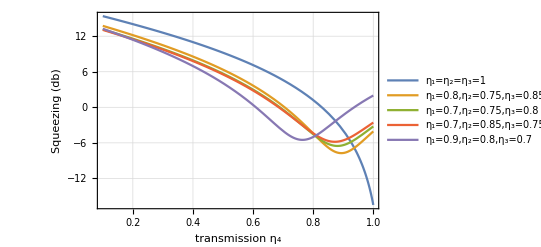

```mathematica
Plot[{10Log10[("48.582"-"94.207" Subscript[η, "4"]+"45.672" Subscript[η, "4"]^("2"))/("1.046"+"1.000" Subscript[η, "4"])](*0.9, 0.9*),10Log10[("30.346"-"67.403" Subscript[η, "4"]+"37.807" Subscript[η, "4"]^("2"))/("0.913"+"1.000" Subscript[η, "4"])](*0.8, 0.7*),10Log10[("26.471"-"59.435" Subscript[η, "4"]+"33.872" Subscript[η, "4"]^("2"))/("0.910"+"1.000" Subscript[η, "4"])],10Log10[("25.990"-"58.807" Subscript[η, "4"]+"33.872" Subscript[η, "4"]^("2"))/("0.910"+"1.000" Subscript[η, "4"])],10Log10[("24.607"-"63.526" Subscript[η, "4"]+"41.740" Subscript[η, "4"]^("2"))/("0.783"+"1.000" Subscript[η, "4"])](*0.8, 0.6*)},{Subscript[η, 4],0.1,1},PlotLegends->{"η_1=η_2=η_3=1","η_1=0.8,η_2=0.75,η_3=0.85","η_1=0.7,η_2=0.75,η_3=0.8","η_1=0.7,η_2=0.85,η_3=0.75","η_1=0.9,η_2=0.8,η_3=0.7"},PlotStyle->Automatic(*PlotRange->{{1,10},{-18,12}}*) (*Y-axis between 0 and 1*),Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Dotted, Gray],AxesLabel->{None,HoldForm["Squeezing (db)"]},FrameLabel->{{HoldForm["Squeezing (db)"],None},{HoldForm["transmission η_4"],HoldForm["R_(ni2 - ns2 - ns1) vs η_4 for G_1= 5.6, G_2= 4.4, α=4"]}},PlotLabel->None,LabelStyle->{GrayLevel[0],Bold}]
```